```mathematica
Computational Physics, Dr. Dell
September 11, 2013
Didi Chang-Park
```

```mathematica
(* Constant acceleration *)
```

```mathematica
s=Manipulate[StreamPlot[{v,a},{x,-5,5},{v,-5,5}, Axes->True],{{a,0.0},-3,3}]
```

```mathematica
(* F=-kx *) 

s1 = Manipulate[
StreamPlot[{v,-kbym x},{x,-5,5},{v,-5,5}, StreamPoints -> Fine],
 {{kbym,0.0}, -3, 3}]
```

```mathematica
(* Look at NDSolve tutorials *)
```

```mathematica
?? NDSolve
```

NDSolve[eqns,u,{t,t_min,t_max}] finds a numerical solution to the ordinary differential equations eqns for the function u with the independent variable t in the range t_min to t_max. 
NDSolve[eqns,u,{t,t_min,t_max},{x,x_min,x_max}] finds a numerical solution to the partial differential equations eqns. 
NDSolve[eqns,{u_1,u_2,…},{t,t_min,t_max}] finds numerical solutions for the functions u_i.

Attributes[NDSolve]={Protected}
 
Options[NDSolve]={AccuracyGoal→Automatic,Compiled→Automatic,DependentVariables→Automatic,DiscreteVariables→{},EvaluationMonitor→None,InterpolationOrder→Automatic,MaxStepFraction→1/10,MaxSteps→10000,MaxStepSize→Automatic,Method→Automatic,NormFunction→Automatic,PrecisionGoal→Automatic,StartingStepSize→Automatic,StepMonitor→None,WorkingPrecision→MachinePrecision}

```mathematica
(*Solve differential equations with constant a, plot*)
```

```mathematica
sol1= NDSolve[{v'[t]== 2.0, x'[t]==v[t],x[0]== 1.0,v[0]== 1.0},{x,v},{t,0,10}]
```

{{x→InterpolatingFunction[{{0.,10.}},<>],v→InterpolatingFunction[{{0.,10.}},<>]}}

```mathematica
(* Forms square root function *)
```

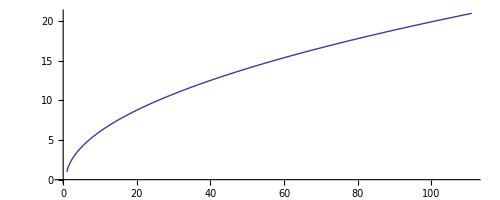

```mathematica
ParametricPlot[{x[t], v[t]}/.First[sol1], {t, 0, 10}]
```

```mathematica
September 12 2013
```

```mathematica
(*  F=-kx *)
```

```mathematica
sol2 = NDSolve[{v'[t]==-1.0x[t], x'[t]==v[t], x[0]==1.0,v[0]==1.0},{x,v},{t,0,10}]
```

{{x→InterpolatingFunction[{{0.,10.}},<>],v→InterpolatingFunction[{{0.,10.}},<>]}}

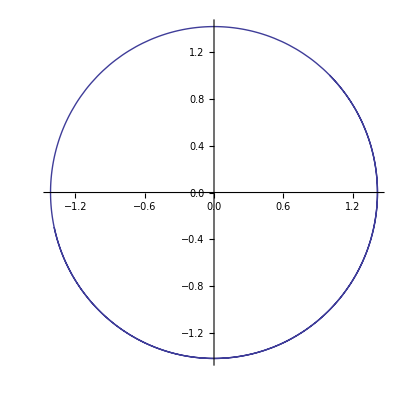

```mathematica
ParametricPlot[{x[t],v[t]}/.First[sol2], {t,0,10}]
```

```mathematica
s = NDSolve[{v'[t]==-4x[t], x'[t]==v[t], x[0]==0, v[0]==1.0},{x,v},{t,0,10}]
```

{{x→InterpolatingFunction[{{0.,10.}},<>],v→InterpolatingFunction[{{0.,10.}},<>]}}

```mathematica
s1 = NDSolve[{v'[t]==-4x[t], x'[t]==v[t], x[0]==0, v[0]==0.0},{x,v},{t,0,10}]
```

{{x→InterpolatingFunction[{{0.,10.}},<>],v→InterpolatingFunction[{{0.,10.}},<>]}}

```mathematica
s2= NDSolve[{v'[t]==-4x[t], x'[t]==v[t], x[0]==0.5, v[0]==0.5},{x,v},{t,0,10}]
```

{{x→InterpolatingFunction[{{0.,10.}},<>],v→InterpolatingFunction[{{0.,10.}},<>]}}

```mathematica
Table[NDSolve[{v'[t]==-4x[t], x'[t]==v[t],x[0]==i,v[0]==j},{x,v},{t,0,10}],{i,2},{j,i}]
```

{{{{x→InterpolatingFunction[{{0.,10.}},<>],v→InterpolatingFunction[{{0.,10.}},<>]}}},{{{x→InterpolatingFunction[{{0.,10.}},<>],v→InterpolatingFunction[{{0.,10.}},<>]}},{{x→InterpolatingFunction[{{0.,10.}},<>],v→InterpolatingFunction[{{0.,10.}},<>]}}}}

```mathematica
(* This function produces a flow with different starting conditions. *)
```

```mathematica
f[a_, b_]:= NDSolve[{v'[t]==-4x[t], x'[t]==v[t],x[0]==a,v[0]==b},{x,v},{t,0,10}]
```

```mathematica
(*This is a table of starting conditions in the form {x,v}. *)
```

```mathematica
t1 = Table[{i,j},{i,-2,2,0.5},{j,-2,2}]
```

{{{-2.,-2},{-2.,-1},{-2.,0},{-2.,1},{-2.,2}},{{-1.5,-2},{-1.5,-1},{-1.5,0},{-1.5,1},{-1.5,2}},{{-1.,-2},{-1.,-1},{-1.,0},{-1.,1},{-1.,2}},{{-0.5,-2},{-0.5,-1},{-0.5,0},{-0.5,1},{-0.5,2}},{{0.,-2},{0.,-1},{0.,0},{0.,1},{0.,2}},{{0.5,-2},{0.5,-1},{0.5,0},{0.5,1},{0.5,2}},{{1.,-2},{1.,-1},{1.,0},{1.,1},{1.,2}},{{1.5,-2},{1.5,-1},{1.5,0},{1.5,1},{1.5,2}},{{2.,-2},{2.,-1},{2.,0},{2.,1},{2.,2}}}

```mathematica
Map[f,t1,{2}]
```

{{f[{-2.,-2}],f[{-2.,-1}],f[{-2.,0}],f[{-2.,1}],f[{-2.,2}]},{f[{-1.5,-2}],f[{-1.5,-1}],f[{-1.5,0}],f[{-1.5,1}],f[{-1.5,2}]},{f[{-1.,-2}],f[{-1.,-1}],f[{-1.,0}],f[{-1.,1}],f[{-1.,2}]},{f[{-0.5,-2}],f[{-0.5,-1}],f[{-0.5,0}],f[{-0.5,1}],f[{-0.5,2}]},{f[{0.,-2}],f[{0.,-1}],f[{0.,0}],f[{0.,1}],f[{0.,2}]},{f[{0.5,-2}],f[{0.5,-1}],f[{0.5,0}],f[{0.5,1}],f[{0.5,2}]},{f[{1.,-2}],f[{1.,-1}],f[{1.,0}],f[{1.,1}],f[{1.,2}]},{f[{1.5,-2}],f[{1.5,-1}],f[{1.5,0}],f[{1.5,1}],f[{1.5,2}]},{f[{2.,-2}],f[{2.,-1}],f[{2.,0}],f[{2.,1}],f[{2.,2}]}}

```mathematica
x[t]/.First[f[0.5,0.5]]
```

InterpolatingFunction[{{0.,10.}},<>][t]

```mathematica
(* define x and v *)
```

```mathematica
xg[a_,b_]:=x[t]/.First[f[a,b]]
```

```mathematica
vg[a_,b_]:=v[t]/.First[f[a,b]]
```

```mathematica
Table[v[t]/.First[f[x0,v0]],{x0,5,0.5},{v0,5,0.5}]
```

{}

```mathematica
l = {{x[t]/.First[s],v[t]/.First[s]},{x[t]/.First[s1],v[t]/.First[s1]},{x[t]/.First[s2],v[t]/.First[s2]}};
```

```mathematica
(*Need to draw trajectories for all possible initial conditions. *well, maybe 0.5 steps or something
Start with fixed acceleration function
How to do this:
	-Use table
   - *)
```

```mathematica
{{x[t]/.First[s],v[t]/.First[s]},{x[t]/.First[s1],v[t]/.First[s1]},{x[t]/.First[s2],v[t]/.First[s2]}}
```

```mathematica
r1 = RandomReal[{-1,1},{3}]*2
```

{-1.67775,1.64419,1.40925}

```mathematica
r2 = RandomReal[{-1,1},{3}]*2
```

{0.128658,-1.56869,0.918662}

```mathematica
pos = Transpose[{r1,r2}]
```

Transpose::nmtx: The first two levels of the one-dimensional list {r1, r2} cannot be transposed.

Transpose[{r1,r2}]

```mathematica
pos[[1]][[1]]
```

-0.0574053

```mathematica
makePoints = Function[{a},NDSolve[{v'[t]==-4x[t], x'[t]==v[t],x[0]==a[[1]],v[0]== a[[2]]},{x,v},{t,0,10}]]
```

Function[{a},NDSolve[{v'[t]==-4 x[t],x'[t]==v[t],x[0]==a⟦1⟧,v[0]==a⟦2⟧},{x,v},{t,0,10}]]

```mathematica
Animate[
	StreamPlot[{v,-4x},{x,-5,5},{v,-5,5},
			Epilog->{Red,Point[
			{ x[t]/.First[makePoints[pos[[1]]]],v[t]/.First[makePoints[pos[[1]]]]}
			], PlotRange->{{-5,5},{-5,5}} ,AspectRatio->1}]
		       ,{t,0,4/2Pi},AnimationRunning->False
	      ]
```

```mathematica
i = Interpretation[{a=5,b=5},Panel[Grid[{
{Style["Initial conditions",Bold],SpanFromLeft},
{"x0:",InputField[Dynamic[a],FieldSize->{{20,Infinity},{1,Infinity}}]},
{"v0:",InputField[Dynamic[b]]}}]],s = NDSolve[{v'[t]==-4x[t], x'[t]==v[t], x[0]== a, v[0]==b},{x,v},{t,0,10}]]
```

{{x→InterpolatingFunction[{{0.,10.}},<>],v→InterpolatingFunction[{{0.,10.}},<>]}}

```mathematica
asdf = NDSolve[{v'[t]==Sin[x[t]], x'[t]==Cos[t],x[0]==1,v[0]==1},{x,v},{t,0,10}]
```

{{x→InterpolatingFunction[{{0.,10.}},<>],v→InterpolatingFunction[{{0.,10.}},<>]}}

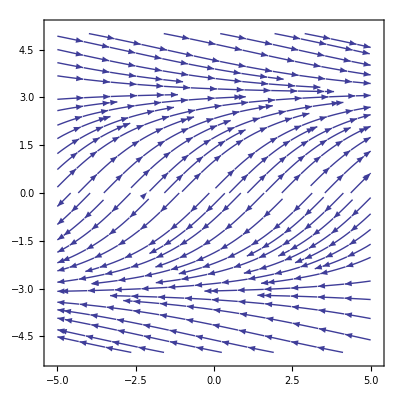

```mathematica
StreamPlot[{v,Sin[v]},{x,-5,5},{v,-5,5}, Axes->True]
```